## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

Import the data. Caution! This takes a while as the file is ~300MB.

```mathematica
data=Import["alloutput_raw.csv",Path->pathBase,HeaderLines->1];
```

Define function functions for accessing the data.

```mathematica
meb[i_]:=data[[i,4;;4099]];
subject[i_]:=data[[i,1]];
imgcode[i_]:=data[[i,2]];
isFA[r_]:=r[[2]]=="fa";
isFB[r_]:=r[[2]]=="fb";
isRC[r_]:=r[[2]]=="rc";
isTrue[r_]:=r[[2]]=="true";
```

```mathematica
0.05316517436375063^2
```

0.00282654

```mathematica
data[[1,3]]
```

00749_941201_fa_var_1106.jpeg

```mathematica
meb[1]
```

{0,0,0,0,0,0,4.61214,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.72292,0,0,0,0,0,6.02955,0,0,0,0.191374,0,0,0,0,0,0,0,0,0,0,0,0,9.08617,3.70566,2.0585,0,0,0,0,0,1.56414,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.58111,0,0,0,0,0,0,0,0,0,8.9522,3.43486,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.81209,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.112609,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.49242,0,0,0.689483,2.17333,1.8004,0,0,0,0,0,0,0,0,0,0,0,0,8.28213,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.540571,0,0,5.91933,0,0,0,0,0,0,0,0,0,0,0,0.452517,0,0,0,0,0,0,0,6.69344,0,0,0,0,0,0,0,0,3.08988,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.633224,0,0,0,0,0,5.28288,0,0,3.07495,0,0,0,0,7.49552,0,8.25591,0,0,0,0,0,0,0,1.13657,0,0.651241,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.43855,0,0,0,0,0,0,0,0,0,0.533267,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.6004,0,1.68138,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.448901,0,0,0,0,0,0,0,0,2.2759,0,13.2277,0,0,0,0,0,0,0,0,0,0,0,2.71383,0,0,0,0,4.68115,0,0,2.46101,0,0,0,0,0,0,0,0.119809,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.9919,0,0,0,0,0,0,0,0,0,0,0,0,0,1.84051,0,0,0,0,0,0,0,0.111356,0,0,0,0,6.15782,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7.82309,0,0,3.03223,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.89494,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.98079,4.55469,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.568137,0,0,0,0,0,0,0,0,0,12.6385,0,0,0,0,0,0,0,0,0,0,0,7.75716,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.96865,0,0,0,0,0,0,3.79926,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.76701,0,11.3926,0,0,0,0,0,0,0,0.0353297,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.11676,0,0,0,0,0,5.06403,0,0,0,2.42132,0,1.89041,0,0,0,0,0,0,0.959009,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.30824,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.62546,0,0,0,0,0,6.3789,0,0,0,0,0,0,0,4.58543,0,0,0,0,8.18631,0,0,0,0,0,0,0.146798,0,0,5.88404,0,0,0,0,0.17576,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.05844,0.381682,0,0,0,3.02786,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.288673,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7.0384,0,0,0,0,0,10.3527,0,0,0,0,0.0970682,0,0,0,0,0,0,1.42369,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.263505,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.70438,0,4.80419,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.47325,0,0,0,1.79662,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.633786,3.73448,0,0,0,0,0,1.26436,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.34031,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7.01336,0,0,0,0,0,0,0,0,0,5.56439,0,0,0,0,6.37637,0,0,1.22042,15.8125,0,0,0,0,0,0,6.73116,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7.15643,0,0,0,0,0,0,9.42288,0,0,0.444117,0,0,0,0,9.41453,0,0,0,0,0,0,0,0,0,4.7381,0,0,1.05219,3.83431,0,0,0,3.82701,3.08954,0,0,0,0,0,0,0,0,0,5.34838,0,0,0,0,0,0,0,0,0,0.536234,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.4061,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.323473,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.27718,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.36129,0,0,0,0,0,0,0,0,0,0,11.6275,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8.8565,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.24337,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.40958,0,0,0,0,0,0,2.75755,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.87618,0,0,0,0,0,0,0,0,0,1.61512,11.6566,4.33522,0,0,0,0,0,0,0,0,0,0,0,0,3.59563,0,0,0,0,8.77794,0,4.34374,0,0,0,0,0,0,0,0,0,0,0,0,9.99243,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.71235,0,0.345224,0,0,0,0,0,0,0,0,2.59187,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8.64728,0,0,0,0,8.34019,0,0,0,0,0,0.834623,0,0,3.0105,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.471065,0,0,1.83462,0,0,3.18199,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.995198,0,0,0,0,0,0,0,0,0.599161,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.3517,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.35027,0,0,0,0,1.73371,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.31413,0,0,0,0,0,0,0,0,0,0,0,0.459163,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.08466,0,0,0,0,0,0,5.62185,0,0,0,0,1.73028,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.45037,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.252414,0,0,0,0,0,0,5.27174,0,0,0,0,0,0,0,1.00543,0,0,0,0,0,2.72902,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.793638,0,0,0,0,0,0,0,0,0,4.87067,0,0,0,0,0,0,0.507682,0,0,0,0.444134,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.65593,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.00707,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.9507,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10.8776,0,0,0,0,0,0,0,3.11885,0,0.898666,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10.517,0,0,0,0,0,0,0,0.0674106,0,0,0,0,0,0,0,0,0,0,0.0554692,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.94011,0,0,0,0,0,13.5884,0,0,5.16833,0,0,0,0,0,0,0,0,0.350543,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.40594,0,0,0,0,4.53188,0,0,0,0,0,0,0,0,0,16.4308,2.77033,3.55581,0,0,0,0,0,0,0,12.0967,0,0,0,0,0,0,0,0,6.20954,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.00067,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.710366,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.15586,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.07413,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.21499,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.71648,0,0,0,0,0,0,0,0,0,0,0,0,10.4048,0,0,0,0,0,0,7.55813,0,0,0,0,0,2.81802,0,0,0,0,0,4.1869,0,0,0,0,0,4.41157,0,0,0,0,0,0,0,0,0,0,4.23355,0,0,2.74119,7.5668,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.58618,0,0,0,0,0,0,0,0.906694,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9.06653,0,4.33028,8.05824,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.26173,0,0,0,0,8.84101,12.2508,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.17378,0,0,0,0,0,0,0,0,0,3.7013,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.53018,0,0,1.0889,0,0,0,0,0,0,0,2.54232,6.02492,0,0,0,0,10.3273,0,0,0,0,0,0,0,0,1.46378,0,0,0,0,0,0,0.808937,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.39823,0,1.5525,0,0,0,0,0,0,14.7862,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.51824,0,0,0,0,0,0,0,0.870695,0,0,0,8.07145,0,0,0,1.60104,0,0,0,0,0,0,0,0,0,0,0,0,10.4837,0,0,0,0,0,0,0,0,0,0,0,0.765746,0.260491,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.48818,0,0,0,0,0,2.21504,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.88132,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.903886,0,0,0,0,0,0,0,0,0,0,0,0.420844,0,2.84177,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8.99336,0,0,0,0,0,0,2.30095,0,0,0,0,0,0,0,0,0,0,0,1.81811,7.4942,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.7992,0,0,0,0,0,1.76825,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.371753,0,0,0,3.29117,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.45825,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.68147,0,0,0,0,5.94018,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.0308,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.9657,0.929576,0,0,7.80639,0,0,0,0,0,0,0,1.63367,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.1849,0,0,0,0,0,0,0,0,0,0,2.83088,0,0,0,0,0,0,0.465783,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.1277,0,0,0,0,0,0,0,0,2.37308,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.06305,0.714496,0,0,0,0,0,0,0,0,0,2.54378,0.778448,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.53946,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.45828,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.7501,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.61975,0,0,0,0,0,0,0,0,0,4.50972,0,0,0,1.21095,0,0,0,0,0,0,0,0,0,3.2146,0,0,0,0,0,0,0,0,0,0,0,0,1.4167,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.66395,0,0,0,0,0,6.62479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.867919,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.164051,0,0,0,0,0,0,0,0,0.307957,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.25547,0,0,0,0,0,0,0,0,0,0,2.43176,0,0,0,6.47129,3.19518,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.34166,0,0,0,0,0,0,0,1.89344,0,9.05382,0,2.66909,0,0,0,0,1.69744,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.71313,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.21613,0,0,0,0,0,0.641775,0.971404,0,0,0,0,0,0,0,1.34352,0,0,0,0,0,0,0,0,0,11.8125,0,5.69432,0,3.01019,0,0,0,0,0,0,0,0,0,0,0,0,0,10.3987,0,0.383064,0,0,0,0,0,0,0,0,0,0,0.409876,0,1.54997,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.61767,0,0,0,0,0,0,0,0,0,0,0,1.54671,0,0,0,0.142614,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.84345,0,0,2.51518,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.26317,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11.8198,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.596666,0,0,0.0797498,4.92138,0,0,0,0,0,0,0,4.12999,3.17124,0,0,0,0,0,0,0}

```mathematica
meb[1]/Norm[meb[1]]
```

{0.,0.,0.,0.,0.,0.,0.0531652,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0544422,0.,0.,0.,0.,0.,0.069504,0.,0.,0.,0.00220601,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.104738,0.042716,0.0237288,0.,0.,0.,0.,0.,0.0180302,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0528075,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.103194,0.0395944,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0669973,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00129807,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0287307,0.,0.,0.00794783,0.0250525,0.0207536,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.09547,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00623128,0.,0.,0.0682334,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00521627,0.,0.,0.,0.,0.,0.,0.,0.0771568,0.,0.,0.,0.,0.,0.,0.,0.,0.0356177,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00729932,0.,0.,0.,0.,0.,0.0608969,0.,0.,0.0354456,0.,0.,0.,0.,0.0864025,0.,0.0951677,0.,0.,0.,0.,0.,0.,0.,0.0131015,0.,0.007507,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0626914,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00614709,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0299754,0.,0.0193816,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00517458,0.,0.,0.,0.,0.,0.,0.,0.,0.0262348,0.,0.152479,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0312829,0.,0.,0.,0.,0.0539607,0.,0.,0.0283686,0.,0.,0.,0.,0.,0.,0.,0.00138107,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0229611,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.021216,0.,0.,0.,0.,0.,0.,0.,0.00128363,0.,0.,0.,0.,0.0709826,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0901785,0.,0.,0.0349532,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0448978,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0113058,0.0525029,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00654904,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.145687,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0894185,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0572747,0.,0.,0.,0.,0.,0.,0.0437949,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0203687,0.,0.131325,0.,0.,0.,0.,0.,0.,0.,0.000407253,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.058982,0.,0.,0.,0.,0.,0.0583742,0.,0.,0.,0.0279111,0.,0.0217912,0.,0.,0.,0.,0.,0.,0.0110547,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0611893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0533187,0.,0.,0.,0.,0.,0.073531,0.,0.,0.,0.,0.,0.,0.,0.0528573,0.,0.,0.,0.,0.0943654,0.,0.,0.,0.,0.,0.,0.00169217,0.,0.,0.0678267,0.,0.,0.,0.,0.00202603,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0467826,0.00439973,0.,0.,0.,0.0349028,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0033276,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0811332,0.,0.,0.,0.,0.,0.119338,0.,0.,0.,0.,0.00111893,0.,0.,0.,0.,0.,0.,0.0164112,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00303748,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0196468,0.,0.055379,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0169825,0.,0.,0.,0.02071,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00730579,0.0430482,0.,0.,0.,0.,0.,0.0145746,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0269773,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0808446,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.064142,0.,0.,0.,0.,0.0735019,0.,0.,0.0140681,0.182274,0.,0.,0.,0.,0.,0.,0.0775916,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0824938,0.,0.,0.,0.,0.,0.,0.10862,0.,0.,0.00511944,0.,0.,0.,0.,0.108523,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0546171,0.,0.,0.0121288,0.044199,0.,0.,0.,0.0441148,0.0356138,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.061652,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00618129,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0623173,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00372875,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0262496,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0272191,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.134033,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.102091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0143326,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0623574,0.,0.,0.,0.,0.,0.,0.0317869,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0792633,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0186179,0.134368,0.0499731,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0414476,0.,0.,0.,0.,0.101185,0.,0.0500713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.115185,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0658475,0.,0.00397947,0.,0.,0.,0.,0.,0.,0.,0.,0.0298771,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0996791,0.,0.,0.,0.,0.0961392,0.,0.,0.,0.,0.,0.00962089,0.,0.,0.0347027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00543007,0.,0.,0.0211481,0.,0.,0.0366795,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0114719,0.,0.,0.,0.,0.,0.,0.,0.,0.00690666,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0271086,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0155649,0.,0.,0.,0.,0.0199849,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0266755,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00529288,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0125031,0.,0.,0.,0.,0.,0.,0.0648043,0.,0.,0.,0.,0.0199453,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.028246,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00290963,0.,0.,0.,0.,0.,0.,0.0607685,0.,0.,0.,0.,0.,0.,0.,0.0115898,0.,0.,0.,0.,0.,0.031458,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00914844,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0561453,0.,0.,0.,0.,0.,0.,0.00585216,0.,0.,0.,0.00511963,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05367,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0692448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0224862,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.125389,0.,0.,0.,0.,0.,0.,0.,0.0359517,0.,0.0103591,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.121232,0.,0.,0.,0.,0.,0.,0.,0.000777057,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000639406,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0338913,0.,0.,0.,0.,0.,0.156637,0.,0.,0.0595765,0.,0.,0.,0.,0.,0.,0.,0.,0.00404079,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0507883,0.,0.,0.,0.,0.05224,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.189402,0.0319342,0.0409886,0.,0.,0.,0.,0.,0.,0.,0.139441,0.,0.,0.,0.,0.,0.,0.,0.,0.0715788,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0576438,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00818855,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0479055,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0584906,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0370599,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0428407,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.119938,0.,0.,0.,0.,0.,0.,0.0871243,0.,0.,0.,0.,0.,0.0324839,0.,0.,0.,0.,0.,0.0482633,0.,0.,0.,0.,0.,0.0508532,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0488011,0.,0.,0.0315983,0.0872242,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0298115,0.,0.,0.,0.,0.,0.,0.,0.0104517,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.104512,0.,0.0499161,0.0928891,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0721804,0.,0.,0.,0.,0.101912,0.141218,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0250577,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0426657,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0406932,0.,0.,0.012552,0.,0.,0.,0.,0.,0.,0.,0.0293059,0.0694506,0.,0.,0.,0.,0.119045,0.,0.,0.,0.,0.,0.,0.,0.,0.0168733,0.,0.,0.,0.,0.,0.,0.0093248,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0506994,0.,0.017896,0.,0.,0.,0.,0.,0.,0.170444,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175011,0.,0.,0.,0.,0.,0.,0.,0.0100367,0.,0.,0.,0.0930414,0.,0.,0.,0.0184555,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.120848,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00882693,0.00300274,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0517363,0.,0.,0.,0.,0.,0.0255333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0447408,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0104193,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00485116,0.,0.0327577,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.103668,0.,0.,0.,0.,0.,0.,0.0265236,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0209578,0.0863873,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0437942,0.,0.,0.,0.,0.,0.020383,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00428528,0.,0.,0.,0.0379381,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0283368,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0424371,0.,0.,0.,0.,0.0684738,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0234095,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0341863,0.0107154,0.,0.,0.089986,0.,0.,0.,0.,0.,0.,0.,0.0188317,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0136586,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0326322,0.,0.,0.,0.,0.,0.,0.00536919,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0129993,0.,0.,0.,0.,0.,0.,0.,0.,0.027355,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.012254,0.00823616,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0293227,0.00897335,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0523274,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.074446,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0201738,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0763073,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0519846,0.,0.,0.,0.0139589,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0370554,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0163306,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0191807,0.,0.,0.,0.,0.,0.0763654,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0100047,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00189105,0.,0.,0.,0.,0.,0.,0.,0.,0.00354989,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0490538,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0280314,0.,0.,0.,0.074596,0.0368316,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0154656,0.,0.,0.,0.,0.,0.,0.,0.0218261,0.,0.104365,0.,0.0307672,0.,0.,0.,0.,0.0195668,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0428021,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0601275,0.,0.,0.,0.,0.,0.00739788,0.0111976,0.,0.,0.,0.,0.,0.,0.,0.0154871,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.136165,0.,0.0656397,0.,0.0346991,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.119868,0.,0.00441566,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00472473,0.,0.0178669,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0301745,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0178293,0.,0.,0.,0.00164394,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0327771,0.,0.,0.028993,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0376153,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.136249,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0068779,0.,0.,0.000919294,0.0567299,0.,0.,0.,0.,0.,0.,0.,0.0476073,0.0365556,0.,0.,0.,0.,0.,0.,0.}

Generate the mean (average) of each neuron’s activation.

```mathematica
meanFAs=Table[Mean[Select[data,isFA][[All,i]]],{i,4,259}];
```

```mathematica
meanFBs=Table[Mean[Select[data,isFB][[All,i]]],{i,4,259}];
```

```mathematica
meanRCs=Table[Mean[Select[data,isRC][[All,i]]],{i,4,259}];
```

```mathematica
meanTrue=Table[Mean[Select[data,isTrue][[All,i]]],{i,4,259}];
```

Function to create a list of (x,y) pairs where x is the index of the neuron and y is its activation value.

```mathematica
indexate[l_]:=Table[{i,l[[i]]},{i,1,Length[l]}]
```

## Graphs

### Average over All the Subjects

This graph shows the difference between the mean activations across all subjects and the mean of the ground truth (again, across all subjects). 

A better way to explain this is to imagine this process:
1. For each given neuron: find the mean activation value across all subjects for a particular image type and for the ground truth.
2. Find the difference between the mean value of the ground truth and the mean activation value (for the respective image type).
3. For each neuron, graph a point indicating this difference.

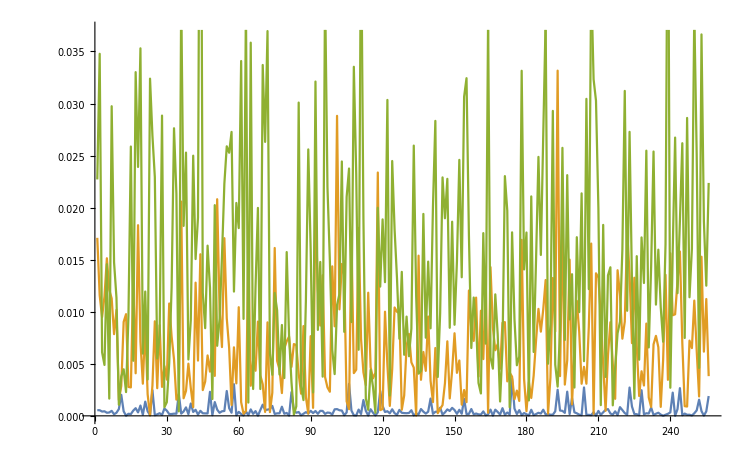

```mathematica
ListLinePlot[indexate/@Abs/@{(meanTrue-meanFAs),(meanTrue-meanFBs),(meanRCs-meanTrue)},AxesOrigin->{0,0}]
```

Comment: Arguably, we are losing a lot of information by averaging out over all subjects. However, some things are clear already. 
1) The difference between the FA’s activations and the ground truth is mostly bounded to <0.001 and definitely by <0.005. So the network is learning the FA’s really well.
2) The FB’s are mostly within 0.015 and some spike up to a difference of 0.030. Again, we are losing a lot of information by averaging out across all subjects. Yet it is clear that the FB’s are further away from the truth than the FA’s.
3) The same can be said for the RC’s -- they are even farther away.

Let’s say we wanted to find out which neuron changes the most from between the RC and the FB activations. This graph could show us just that. 

It plots the difference between the mean FB activation value and the mean RC activation value when the mean is taken across all variations of all subjects.

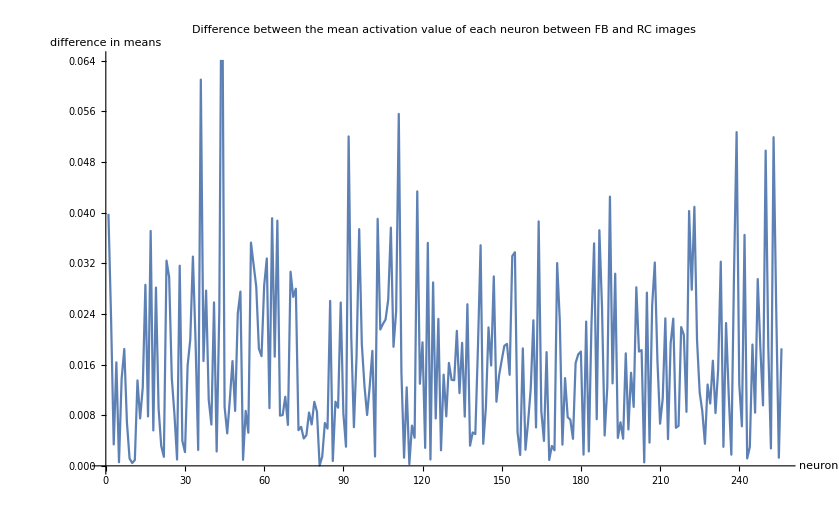

```mathematica
Show[ListLinePlot[indexate/@Abs/@{(meanFBs-meanRCs)},AxesOrigin->{0,0}],AxesLabel->{HoldForm[neuron],HoldForm[difference in means]},PlotLabel->HoldForm[Difference between the mean activation value of each neuron between FB and RC images],LabelStyle->{GrayLevel[0]}]
```

Comment: We are definitely losing information by averaging out everything, yet judging by this graph, the distances do not seem significant.
It would be interesting to:
1) divide by the standard deviation to standardize these differences (or another appropriate statistical technique) 
2) look at a similar plot for one subject only
in order to gain more information

### Focus on Subject 00070

Subject 00070 is interesting because the evaluation achieved 0 matching scores both for the RC’s and for the FB’s. So what went wrong?

First, a quick function that we will use in the selection.

```mathematica
isSubj70[r_]:=r[[1]]==70;
```

```mathematica
dataSubj70=Select[data, isSubj70];
```

```mathematica
subj70True=Select[dataSubj70,isTrue][[1,4;;259]];
meanFA70=Table[Mean[Select[dataSubj70,isFA][[All,i]]],{i,4,259}];
meanFB70=Table[Mean[Select[dataSubj70,isFB][[All,i]]],{i,4,259}];
meanRC70=Table[Mean[Select[dataSubj70,isRC][[All,i]]],{i,4,259}];
```

Let us first plot the (absolute) difference between the real MEB code for subject 70 and the activation values for each neuron for FA, FB, and RC images, respectively.

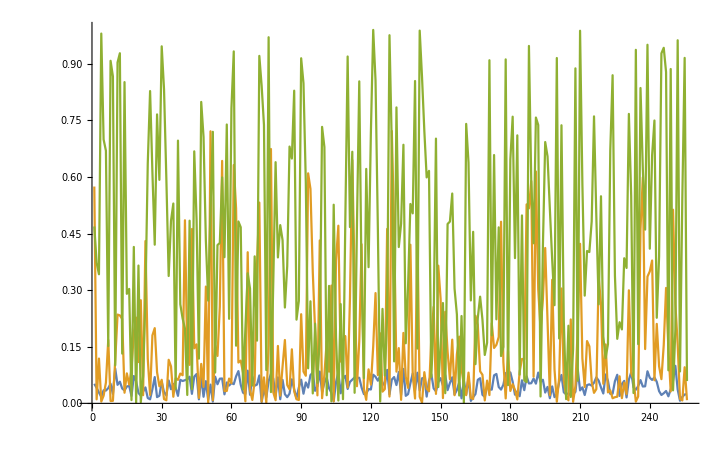

```mathematica
ListLinePlot[indexate/@Abs/@{(subj70True-meanFA70),(subj70True-meanFB70),(subj70True-meanRC70)},AxesOrigin->{0,0}]
```

Comment: Wow. The RC’s are very far off -- with wild variations. Whereas the FA’s are all in a band around 0.02 (we trained on them after all), the FB’s and the RC’s vary wildly. There are many neurons where the RC is not only not close but the exact opposite of what the real MEB is.

Let us now look at the difference between the FB and the RC.

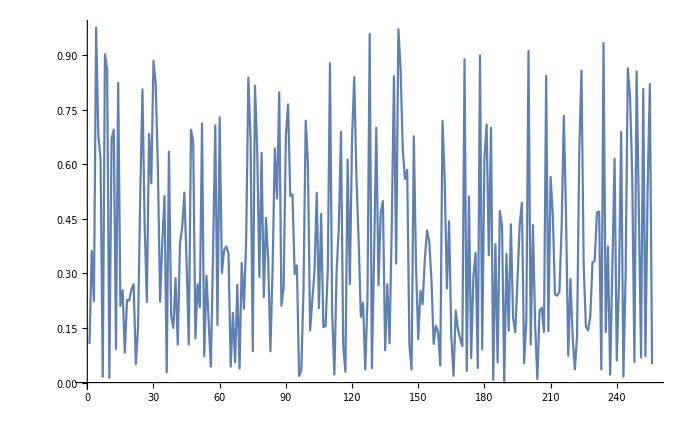

```mathematica
ListLinePlot[indexate/@Abs/@{(meanFB70-meanRC70)},AxesOrigin->{0,0}]
```

Comment: On first glance, it seems like we have a problem -- many neurons shift completely when moving from an RC to an FB. However, I would not jump to that conclusion yet as it seems like the RC is just random noise.

### Focus on Subject ??????

Subject ????? is interesting because the evaluation achieved a really good score on the FB’s but a very low score on the RC’s. So what went wrong when we moved from the FB’s to the RC’s?